# Practical 2 Plotting of second order solution family of differential equation

```mathematica
1.plot the following second order initial value problem y''[x] - 6y'[x]+8y[x]=0,y(0)=1, y'(0)=1
```

{{y[x]→-1/2 ⅇ^(2 x) (-3+ⅇ^(2 x))}}

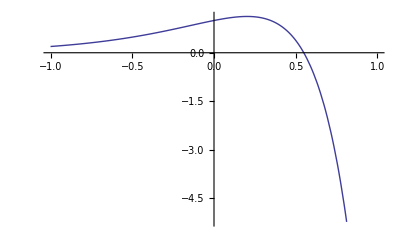

```mathematica
sol = DSolve[ {y''[x] - 6y'[x] + 8y[x]==0,y[0]==1, y'[0]==1},y[x],x]
Plot[y[x]/.sol, {x,-1,1}]
```

```mathematica
2.plot the following second order initial value problem {IVP}2y''[x] +5y'[x] + 3y[x]=0, 
y[0]=3,
y'[0]=-4
```

{{y[x]→ⅇ^(-3 x/2) (2+ⅇ^(x/2))}}

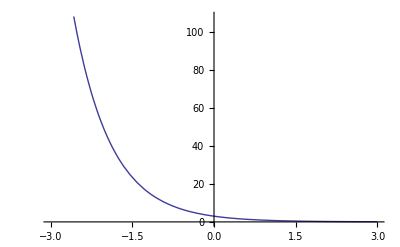

```mathematica
sol = DSolve[{2y''[x] +5y'[x] + 3y[x]==0, y[0]==3,y'[0]==-4}, y[x],x]
Plot[y[x]/.sol,{x,-3,3}]
```

```mathematica
DSolve[y'[x]==Sin[x],y[x],x]
```

{{y[x]→C[1]-Cos[x]}}

```mathematica
3. Solve the following second order initial value problem {IVP}y''[x] + 16y[x] =0,y(Pi/4)=-3, y'(Pi/4)=4
```

```mathematica
sol = DSolve[{y''[x] + 16y[x] ==0, y[π/4]==-3, y'[π/4]==4},y[x],x]
```

{{y[x]→3 Cos[4 x]-Sin[4 x]}}

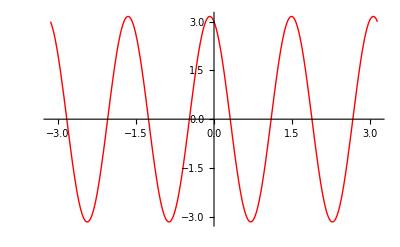

```mathematica
Plot[y[x]/.sol, {x,-Pi,Pi},PlotStyle->{Red}, PlotRange->Full]
```

```mathematica
4. Solve the following second order initial value problem {IVP} 4y''[x] +y[x] ==0,y(0)=3, y(Pi)=-4
```

```mathematica
sol = DSolve[{4y''[x] + y[x]==0,y[0]==3,y[π]==4}, y[x],x]
```

```mathematica
{{y[x]->3 Cos[x/2]+4 Sin[x/2]}}
```

{{y[x]→3 Cos[x/2]+4 Sin[x/2]}}

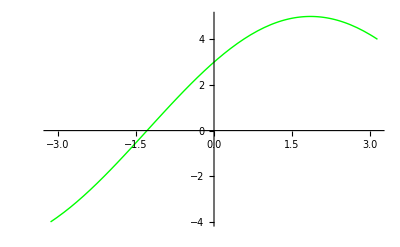

```mathematica
Plot[y[x]/. sol, {x,-π,π}, PlotStyle->{Red, Green}, PlotRange->Full]
```

```mathematica
5. Solve the following second order initial value problem {IVP} y''[x] + 2y'[x] =0, y(0) = 1, y(1) =2
```

```mathematica
sol = DSolve[{y''[x] + 2y'[x]==0, y[0]==1, y[1]==2},y[x],x]
```

{{y[x]→(ⅇ^(-2 x) (-ⅇ^2-ⅇ^(2 x)+2 ⅇ^(2+2 x)))/(-1+ⅇ^2)}}

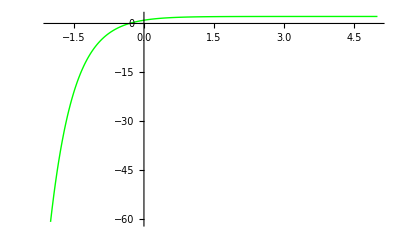

```mathematica
Plot[y[x]/. sol, {x,-2,5}, PlotStyle->{Red, Green}, PlotRange->Full]
```

```mathematica
6. Solve the following second order initial value problem{IVP} y''[x] + 100y[x] =0, y[0]=2, y'[π]=5
```

```mathematica
sol = DSolve [{y''[x] - 6y'[x] +25y[x] ==0, y[0]==1, y'[π]==2},y[x],x]
```

{{y[x]→1/4 ⅇ^(-3 π+3 x) (4 ⅇ^(3 π) Cos[4 x]+2 Sin[4 x]-3 ⅇ^(3 π) Sin[4 x])}}

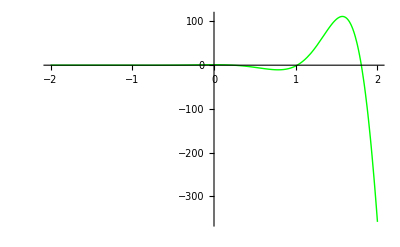

```mathematica
Plot[y[x]/. sol, {x,-2,2}, PlotStyle->{Red, Green}, PlotRange->Full]
```

```mathematica
7. Solve the following second order initial value problem {IVP}y''[x] + 2y'[x] +2y[x]=0,y(0)=2, y'(0)=1
```

```mathematica
sol = DSolve[{y''[x] +2y'[x] + 2y[x]==0, y[0]==2, y'[0]==1},y[x],x]
```

{{y[x]→ⅇ^-x (2 Cos[x]+3 Sin[x])}}

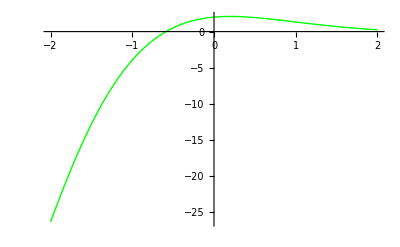

```mathematica
Plot[y[x]/. sol, {x,-2,2}, PlotStyle->{Red, Green}, PlotRange->Full]
```